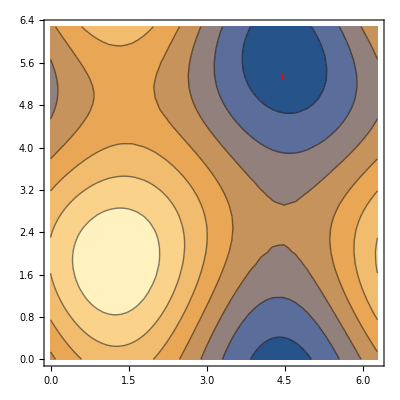

```mathematica
SeedRandom[10];
r=ArrayReshape[RandomReal[{0,1},9,WorkingPrecision->20],{3,3}];
loss[x_,y_]:=Sum[r[[i+1,j+1]] Cos[x/2]^i Sin[x/2]^(2-i)Cos[y/2]^j Sin[y/2]^(2-j),{i,0,2},{j,0,2}]
monoloss[x_,y_]:=Coefficient[(loss[x,y]//FullSimplify)/.{Cos[v_]:>t Cos[v],Sin[v_]:>t Sin[v]},t]
minGuess=Mod[Module[{x,y},{x,y}/.FindMinimum[monoloss[x,y],{x,y},WorkingPrecision->20][[2]]],2π]//N;

Show[ContourPlot[loss[x,y],{x,0,2π},{y,0,2π}],ListPlot[{minGuess},PlotStyle->{Thick,Red},PlotMarkers->"*"]]
```

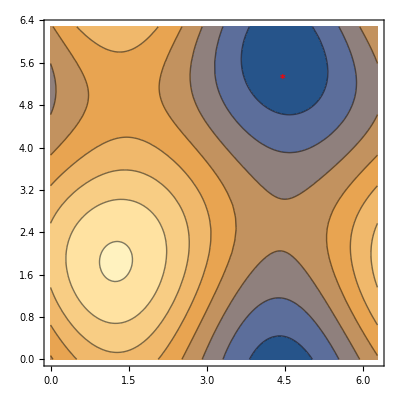

```mathematica
Show[ContourPlot[stryLinv[20],{x,0,2π},{y,0,2π}],ListPlot[{minGuess},PlotStyle->{Thick,Red},PlotMarkers->"*"]]
```

```mathematica
stry=loss[x,y]-0.57769716785875164073476113374456854271`17.74118302113632//FullSimplify//Chop
```

Cos[y] (-0.16226355268402+0.0577582712199865 Sin[x])+Cos[x] (0.105977858490373+0.033933886247093 Cos[y]+0.0613639578132058 Sin[y])+Sin[x] (0.4208521518140327+0.07814924749614423 Sin[y])+0.248287332003948 Sin[y]

```mathematica
stryLinv[n_]:=2^n(-1)^n stry/.{Cos[v_]:>Cos[v]/2^n,Sin[v_]:>Sin[v]/2^n}
```

```mathematica
Laplacian[stryLinv[1],{x,y}]- stry//Simplify//Chop
Laplacian[Laplacian[stryLinv[2],{x,y}],{x,y}]-stry//Simplify//Chop
Laplacian[Laplacian[Laplacian[stryLinv[3],{x,y}],{x,y}],{x,y}]-stry//Simplify//Chop
```

0

0

0

```mathematica
stryLinv[30]//N//Chop//Expand
```

0.105978 Cos[x]-0.162264 Cos[y]+0.420852 Sin[x]+0.248287 Sin[y]

```mathematica
monoloss[x,y]//Chop
```

0.1059778584903725 Cos[x]-0.16226355268402018 Cos[y]+0.42085215181403273 Sin[x]+0.24828733200394796 Sin[y]